# Mathematica Lab 1-Properties Fourier Series Representation

## Property-Time Reversal of a Continuous-Time Periodic Signal (with general explanations) *SCIMATH301 - Signals & Systems* *Joanikij Chulev* *22.09.2022*

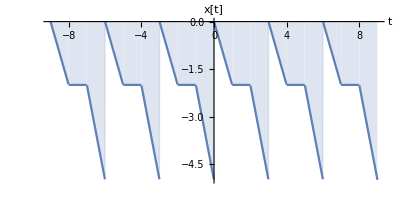

```mathematica
(* This defines the period and each period is also piecewise: *)T=3;
(* This defines a piecewise periodic continuous-time signal: *)
x[t_]:=Piecewise[{{-2Mod[t,T],0≤Mod[t,T]<1},{4-3Mod[t,T],2≤Mod[t,T]<3},{-2,1≤Mod[t,T]<2}}];
(* This plots 6 periods of the periodic signal: *)
Px=Plot[x[t],{t,-3T,3T},PlotRange->All,AspectRatio->1/2,Filling->Axis,AxesLabel->{"t","x[t]"}]
```

(ⅇ^(-2 ⅈ k π) (-9+9 ⅇ^((2 ⅈ k π)/3)-6 ⅇ^((4 ⅈ k π)/3)+6 ⅇ^(2 ⅈ k π)-10 ⅈ k π+4 ⅈ ⅇ^((2 ⅈ k π)/3) k π-4 ⅈ ⅇ^((4 ⅈ k π)/3) k π-8 ⅇ^(ⅈ k π) k π Sin[(k π)/3]))/(4 k^2 π^2)

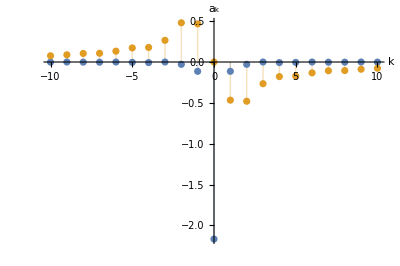

```mathematica
(* This calculates the Fourier Series coefficients: *)
a[k_]=1/T∫_0^T x[t]Exp[-ⅉ k (2π)/T t]ⅆt
(* This is a table of ak's: *)
val=Table[{k,If[k≠0,a[k],Limit[a[kk],kk->0]]},{k,-10,10}];
(* This plots the real and imaginary part of the ak's: *)
Pak=ListPlot[{Transpose[{Transpose[val][[1]],Re[Transpose[val][[2]]]}],Transpose[{Transpose[val][[1]],Im[Transpose[val][[2]]]}]},PlotRange->All,Filling->Axis,AspectRatio->2/3,AxesLabel->{"k","a_k"}]
```

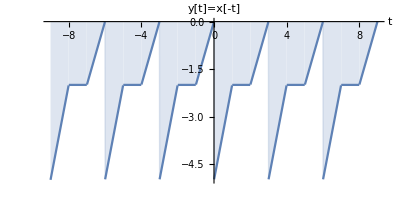

```mathematica
(* THIS TAKES THE REVERSED SIGNAL *)
y[t_]:=x[-t];
Py=Plot[y[t],{t,-3T,3T},PlotRange->All,AspectRatio->1/2,Filling->Axis,AxesLabel->{"t","y[t]=x[-t]"}]
```

(ⅇ^(-2 ⅈ k π) (6-6 ⅇ^((2 ⅈ k π)/3)+9 ⅇ^((4 ⅈ k π)/3)-9 ⅇ^(2 ⅈ k π)+4 ⅈ ⅇ^((2 ⅈ k π)/3) k π-4 ⅈ ⅇ^((4 ⅈ k π)/3) k π+10 ⅈ ⅇ^(2 ⅈ k π) k π-8 ⅇ^(ⅈ k π) k π Sin[(k π)/3]))/(4 k^2 π^2)

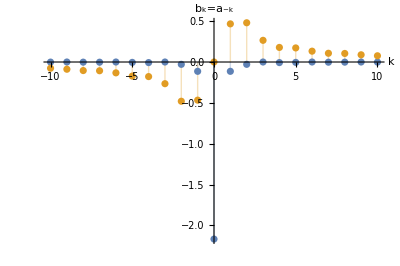

```mathematica
(* This calculates the Fourier Series coefficients: *)
b[k_]=1/T∫_0^T y[t]Exp[-ⅉ k (2π)/T t]ⅆt
(* This is a table of ak's: *)
val2=Table[{k,If[k≠0,b[k],Limit[b[kk],kk->0]]},{k,-10,10}];
(* This plots the real and imaginary part of the ak's: *)
Pbk=ListPlot[{Transpose[{Transpose[val2][[1]],Re[Transpose[val2][[2]]]}],Transpose[{Transpose[val2][[1]],Im[Transpose[val2][[2]]]}]},PlotRange->All,Filling->Axis,AspectRatio->2/3,AxesLabel->{"k","b_k=a_-k"}]
```

```mathematica
(* This checks if the Fourier coefficients are also reversed: *)
Assuming[k∈Integers,Simplify[b[k]==a[-k]]]
```

True

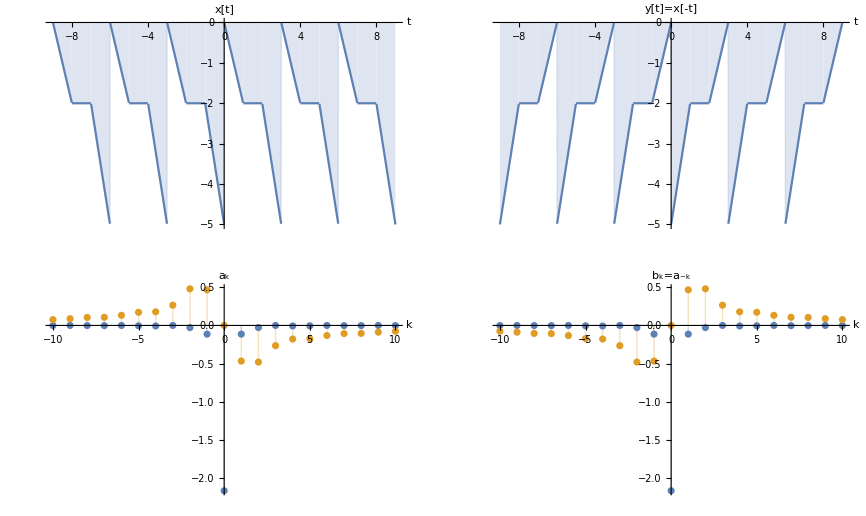

```mathematica
(* This shows all plots in one overview: *)
GraphicsGrid[{{Px,Py},{Pak,Pbk}},Frame->True]
```